```mathematica
(* Evaluate this cell before doing anything else in order to define functions. *)

SetDirectory[NotebookDirectory[]];  (* Sets all path names to be relative to the directory where this notebook is. *)

pairspath="pairshm.mx";

(* Functions one can calculate on each time frame. *)
p[timeframe_]:=("data"/.timeframe)[[1]]
πp[timeframe_]:=("data"/.timeframe)[[2]]
q[timeframe_]:=("data"/.timeframe)[[3]]
πq[timeframe_]:=("data"/.timeframe)[[4]]
λ[timeframe_]:=("data"/.timeframe)[[5]]
πλ[timeframe_]:=("data"/.timeframe)[[6]]
τ[timeframe_]:=("time"/.timeframe)
α[timeframe_]:=1/(2πλ[timeframe])^2
v[timeframe_]:=p[timeframe]+τ[timeframe]
ρ[timeframe_]:=-1/2 Log[α[timeframe]]
l[timeframe_]:=p[timeframe]+1/2λ[timeframe]-3/2τ[timeframe]-Log[2]
Ptau[timeframe_]:=-πp[timeframe]/(2*πλ[timeframe])
Qtau[timeframe_]:=-Exp[-2p[timeframe]]πq[timeframe]/(2*πλ[timeframe])
λtau[timeframe_]:=1/(2*πλ[timeframe])^2(πp[timeframe]^2+Exp[-2p[timeframe]]πq[timeframe]^2+Exp[-2τ[timeframe]]spacederivative[p,timeframe]^2+Exp[2(p[timeframe]-τ[timeframe])]spacederivative[q,timeframe]^2)+Exp[(λ[timeframe]+2p[timeframe]+3τ[timeframe])/2]
Vtau[timeframe_]:=Ptau[timeframe]+1
ρtau[timeframe_]:=Exp[l[timeframe]]
A[timeframe_]:=Mean[-πp[timeframe]+2πλ[timeframe]+q[timeframe]*πq[timeframe]];
B[timeframe_]:=Mean[-πq[timeframe]];
c[tf_]:=Mean[(Qtau[tf]-2q[tf]+q[tf]Vtau[tf])2 πλ[tf]+q[tf](-πp[tf]+2πλ[tf]+q[tf]*πq[tf])];

(* Computes a finite-difference spatial derivative of a function on a time frame. *)
spacederivative=
Function[{f,timeframe},
Module[{temp,n,Δx},
temp=f[timeframe];
n=Length[temp];
Δx=2 Pi / n;
temp=Join[
{temp[[n-1]]},
{temp[[n]]},
temp,
{temp[[1]]},
{temp[[2]]}
];
Table[(2/3*(temp[[i+1]]-temp[[i-1]])+1/12*(temp[[i-2]]-temp[[i+2]]))/Δx,{i,1+2,n+2}]
]
];

(* Calculate the constraint. Note that this is pointwise in space. This should be identically 0 for solutions without error. *)
galconstraint[tf_]:=Module[{dp,dq,dλ},
 dp=spacederivative[p,tf];
 dq=spacederivative[q,tf];
 dλ=spacederivative[λ,tf];
(dp*πp[tf])+(dq*πq[tf])+(dλ*πλ[tf])
]
galconstraintavg[tf_]:=Mean[galconstraint[tf]]

(* More functions that can be computed on time frames. *)
Ev[tf_]:=Vtau[tf]^2+Exp[2(τ[tf]-ρ[tf])]spacederivative[p,tf]^2
Eq[tf_]:=Exp[2(v[tf]-τ[tf])](Qtau[tf]^2+Exp[2(τ[tf]-ρ[tf])]spacederivative[q,tf]^2)
En[tf_]:=Ev[tf]+Eq[tf]
J[tf_]:=1/2 En[tf]
mE[tf_]:=Mean[Exp[ρ[tf]-2τ[tf]] J[tf]]
Π[tf_]:=Mean[Exp[ρ[tf]] ]
Λ[tf_]:=1/2Mean[Exp[-2τ[tf]+ρ[tf]]Vtau[tf](v[tf]-Mean[v[tf]]-1)]
H[tf_]:=Π[tf](mE[tf]+Λ[tf])
Y[tf_]:=Mean[Exp[l[tf]+ρ[tf]+2τ[tf]]]
cc[tf_]:=Π[tf]Exp[-τ[tf]]H[tf]^(-1/2)
dd[tf_]:=Y[tf]Exp[-3τ[tf]]H[tf]^(-1/2)

ltau[tf_]:=-2-ρtau[tf]+1/2En[tf]

(* The terms from Beverly's superhamiltonian. The 'a' versions below just have an extra factor of 1/πλ so that they are O(1) generically. *)
H0[timeframe_]:=πp[timeframe]*πp[timeframe]/(4*πλ[timeframe])
Hkin[tf_]:=Exp[-2 p[tf]] πq[tf]*πq[tf]/(4*πλ[tf])
Hsmall[tf_]:=Exp[2 τ[tf]] spacederivative[p,tf]*spacederivative[p,tf]/(4*πλ[tf])
Hcurv[tf_]:=Exp[2 τ[tf]]Exp[2 p[tf]]spacederivative[q,tf]*spacederivative[q,tf]/(4*πλ[tf])
Htwist[tf_]:=πλ[tf] Exp[-3τ[tf]/2]Exp[λ[tf]/2+p[tf]]

H0a[timeframe_]:=πp[timeframe]*πp[timeframe]/(4*πλ[timeframe]*πλ[timeframe])
Hkina[tf_]:=Exp[-2 p[tf]] πq[tf]*πq[tf]/(4*πλ[tf]*πλ[tf])
Hsmalla[tf_]:=Exp[2 τ[tf]] spacederivative[p,tf]*spacederivative[p,tf]/(4*πλ[tf]*πλ[tf])
Hcurva[tf_]:=Exp[2 τ[tf]]Exp[2 p[tf]]spacederivative[q,tf]*spacederivative[q,tf]/(4*πλ[tf]*πλ[tf])
Htwista[tf_]:= Exp[-3τ[tf]/2]Exp[λ[tf]/2+p[tf]]

(* This is the function that takes a path to a json file and turns the result into a Mathematica-friendly form. DO NOT USE THIS FUNCTION DIRECTLY. Use the function apnp defined below instead. *)
myimport[path_]:=Block[{text,timeframes},
(* There is a bug with importing json floats of length greater than 19. See https://mathematica.stackexchange.com/questions/163825/problem-to-import-numbers-longer-than-19-digit-with-json-or-rawjson *)
Import[path,"Text"]//StringReplace[{"{"->"<|","}"->"|>",":"->"->","["->"{","]"->"}","e+"~~s_:>" 10^"~~s,"e-"~~s_:>" 10^-"~~s}]//ToExpression
]

(* Returns a nice (x,y) table after applying the function f to all the time frames. *)
ClearAll[pairs];
pairs[file_,f_]:=Block[{data,timeframes},
data=file//myimport;
 (* +++++++++++++++++++++++++++++++++++++
NOTA BENE: I use the operator // a lot in my coding.
The meaning is this: x//f//g == g[f[x]] analogous to the pipe | in *nix shells.
Closely related is the /* operator: f/*g is the function which is the composition of f and g.
That is, (f/*g)[x] = g[f[x]].
The difference is that f/*g can be passed around as a function, while f//g cannot; the latter must be applied to some input.
+++++++++++++++++++++++++++++++++++++ *)
timeframes=("evolution"/.data);
Table[{τ[i],f[i]},{i,timeframes}]//Sort[#,#1[[1]]<#2[[1]]&]&
]

(* Return a list of all the json files in the same directory as the input. *)
files=Function[file,
Module[{root,dir},
dir=DirectoryName[file];
root=FileBaseName[file];
FileNames[root<>".*.json",{dir}]
]
];

(*$HistoryLength=0;*)

(* The next few functions are related to actually getting data out of json files. Part of the complexity is related to memoization. There is the logic: 
  1) myimport gets data from a file and returns it as an array, but it doesn't memoize what is returned, so if we keep re-evaluating the same function on the same file, it takes the time to read the file from disk each time.
  2) pairshm is a memoized version of myimport: if we call it on the same file with the same function, it doesn't read the file again. The line <<pairspath; reads previously memoized values from a file when we open the notebook again.
  3) The underlying files might change (as we evaluate for longer times) so we want to load them anew if they have changed, so pairsm gets the size and date of the file and makes pairshm get it again if these values have chaged.
  4) All the previous functions only act on a single file, but the data may be split up between many files. The function apnp looks for other files in the same directory for the given run and loads the data for all of them, then combines it and sorts by time. This is the function you should actually call to get a list of time frames.
*)

ClearAll[pairshm];
Get[pairspath];
pairshm[file_,f_,size_,date_]:=pairshm[file,f,size,date]=Block[{data,timeframes},
PrintTemporary[file];
pairshm//DownValues//Map[#[[1]]&]//Select[StringMatchQ[ToString[#],___~~file~~___]&]//Select[StringMatchQ[ToString[#],___~~ToString[f]~~___]&]//Map[(#=.)&]; (* Clear previous memoizations for this function and file if they exist. *)
data=file//myimport;
timeframes=("evolution"/.data);
Table[{τ[i],f[i]},{i,timeframes}]
]

ClearAll[pairsm];
pairsm[file_,f_]:=pairshm[file,f,file//FileByteCount,file//FileDate//UnixTime];

files2=Function[file,
Module[{root,dir,reses,filenames},
dir=DirectoryName[file];
root=FileBaseName[file];
filenames=FileNames[root<>"_*.*.json",{dir}];
reses=filenames//Map[StringReplace[__~~"_"~~s__~~"."~~__~~".json":>s]]//Union//SortBy[ToExpression[#]&];
reses//Map[Select[filenames,StringMatchQ[dir~~root~~"_"~~#~~"."~~__~~".json"]]&]
]
];

ClearAll[apnp];
apnp[file_,f_]:=Block[{files,out},
files=files2[file]//Flatten;
out=Table[
j->pairsm[j,f]
,{j,files}]//Flatten[#,1]&;
(files2[file]/.out)//Map[Flatten[#,1]&]//Map[SortBy[#[[1]]&]]
]

dir="../long_runs/"; (* for the notebook, set the location where the runs are stored. Leave this as "../long_runs/" if you are running this notebook from the folder in the cloned git repo. *)
resolutions=Range[2,3]; (* Which resolutions to look for. 1 -> 512 , 2 -> 1024 , ... *)
twidth=4; (* When generating tables of plots, how many columns should there be? *)
```

58

{b0_0,gen_0,b0_9,b0_13,b0_24,b0_26,b0_43,b0_58,b0_61,b0_64,b0_81,b0_85,b0_89,b0_121,b0_139,b0_162,b0_172,b0_179,b0_180,b0_190,gen_9,gen_13,gen_24,gen_43,gen_58,gen_61,gen_64,gen_69,gen_81,gen_85,gen_90,gen_121,gen_139,gen_156,gen_162,gen_163,gen_172,gen_179,gen_190,gen_192,pol_3,pol_90,pol_104,pol_105,pol_107,pol_108,pol_113,pol_124,pol_131,pol_144,pol_151,pol_164,pol_167,pol_168,pol_186,pol_193,pol_196,pol_197}

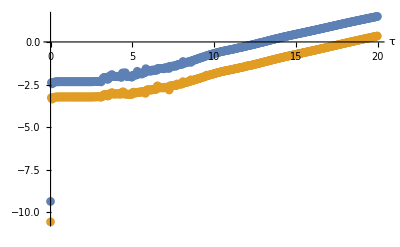
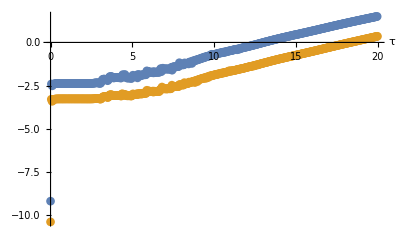
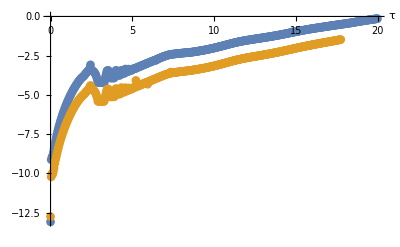
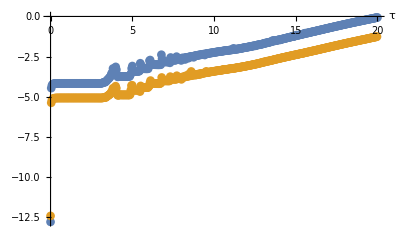
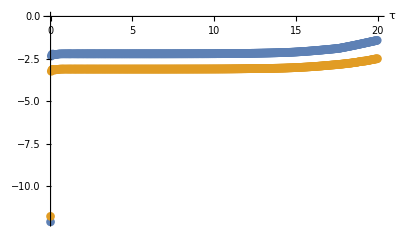
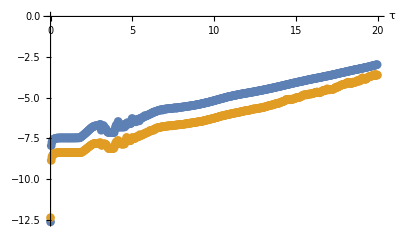
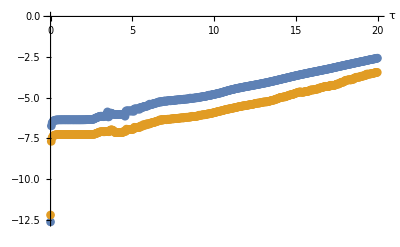
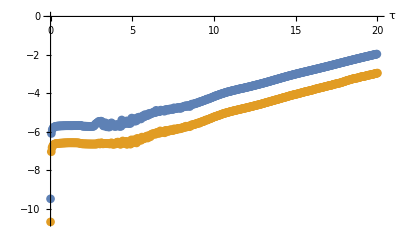
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Module[{type,filenames,runs,filess,k,print,i},
filenames=FileNames["*t_*.1.json",{dir}];
i=0;
runs=filenames//StringReplace[dir<>"t_"~~typeandnum__~~"_"~~__~~".json"->typeandnum]//Union//SortBy[ToExpression[#]&]//#[[;;]]&;
Print[runs//Length];
Print[runs];
Module[{tmp},
tmp=
Monitor[
Table[  (* For each run... *)
{
filee
,apnp[  (* ... get all the data from all the files ... *)
dir<>"t_"<>filee<>".json"
,{
galconstraint/*Abs/*Max/*Log10
,1/Π[#]Mean[Exp[ρ[#]]Ev[#]]&
,1/Π[#]Mean[Exp[ρ[#]]Eq[#]]&
,Mean[(l[#]-Log[1/2])]Exp[τ[#]/4]&
,Mean[(ρ[#]-τ[#]/2)Exp[ρ[#]]]/Mean[Exp[ρ[#]]]&
}[[1]] (* ... and apply the function I select from this little list ... *)
]//ListPlot[  (* ... then plot it ... *)
#[[resolutions]]//Map[Select[#[[1]]≤20&]]
,PlotRange->{All,All}
,PlotStyle->PointSize[1/64]
,ImageSize->Scaled[1/twidth ]
,Epilog->Inset[Framed[filee,Background->LightYellow],ImageScaled[{.8,.2}]] (* ... with a nice label of the name of the run ... *)
,AxesLabel->{"τ",""}
]&
}
,{filee,runs}
]
,{ProgressIndicator[FirstPosition[runs,filee][[1]]-1,{0,runs//Length},ImageSize->Scaled[1/2]],filee}];(*
tmp//Map[Export[#[[1]]<>"_rho.png",#[[2]],ImageSize->1000]&];*) (* uncomment the stuff to the left if you'd like to write images of the plots to the disk. *)
tmp//Map[#[[2]]&]
]//Partition[#,UpTo[twidth]]&//TableForm (* ... and make a nice grid of all the plots for the runs. *)
]

Module[{path=pairspath},
DumpSave[path,pairshm];
]
```